```mathematica
Select[ListofVars[allGraphs5[0,"colofour"]],StringCount[SymbolName[#],"x"]==1&]
```

{v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],With[{v=ListofVars[allGraphs5[#,"colofour"]]},MemberQ[v,v1234x5]&&MemberQ[v,v12345]]&]}]//Length
```

15

```mathematica
Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],With[{v=ListofVars[allGraphs5[#,"colofour"]]},MemberQ[v,v1235x4]&&MemberQ[v,v12345]]&]}]//Length
```

15

```mathematica
DeleteDuplicates[Union[Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],With[{v=ListofVars[allGraphs5[#,"colofour"]]},MemberQ[v,v1235x4]&&MemberQ[v,v12345]]&]}],Table[Labeled[allGraphs5[k,"graph"],k],{k,Select[Keys[allGraphs5],With[{v=ListofVars[allGraphs5[#,"colofour"]]},MemberQ[v,v1234x5]&&MemberQ[v,v12345]]&]}]]]//Length
```

25

```mathematica
Fold[Or,Table[MemberQ[vars,m],{m,{v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345}}]]
```

False

```mathematica
base1=Append[Select[Keys[allGraphs5],With[{vars=ListofVars[allGraphs5[#,"colofour"]]},
MemberQ[vars,v12345]&&Fold[Or,Table[MemberQ[vars,m],{m,{v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345}}]]]&]
,59048]
```

{0,39366,52974,57528,54492,52976,43902,45416,43908,40878,40896,39384,39392,39372,39368,13122,17514,18980,17568,14586,14748,13284,13340,13176,13124,4374,5834,6320,4860,4920,4428,4380,1458,1944,2124,1620,1476,486,666,728,546,488,162,218,168,54,72,18,26,6,2,59048}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],{k,base1}]
```

{-Graphics-0,-Graphics-39366,-Graphics-52974,-Graphics-57528,-Graphics-54492,-Graphics-52976,-Graphics-43902,-Graphics-45416,-Graphics-43908,-Graphics-40878,-Graphics-40896,-Graphics-39384,-Graphics-39392,-Graphics-39372,-Graphics-39368,-Graphics-13122,-Graphics-17514,-Graphics-18980,-Graphics-17568,-Graphics-14586,-Graphics-14748,-Graphics-13284,-Graphics-13340,-Graphics-13176,-Graphics-13124,-Graphics-4374,-Graphics-5834,-Graphics-6320,-Graphics-4860,-Graphics-4920,-Graphics-4428,-Graphics-4380,-Graphics-1458,-Graphics-1944,-Graphics-2124,-Graphics-1620,-Graphics-1476,-Graphics-486,-Graphics-666,-Graphics-728,-Graphics-546,-Graphics-488,-Graphics-162,-Graphics-218,-Graphics-168,-Graphics-54,-Graphics-72,-Graphics-18,-Graphics-26,-Graphics-6,-Graphics-2,-Graphics-59048}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],{k,allGraphs5NullAtomKeys}]
```

{-Graphics-0,-Graphics-39366,-Graphics-52974,-Graphics-57528,-Graphics-59048,-Graphics-54492,-Graphics-52976,-Graphics-43902,-Graphics-45416,-Graphics-43908,-Graphics-40878,-Graphics-40896,-Graphics-39384,-Graphics-39392,-Graphics-39372,-Graphics-39368,-Graphics-13122,-Graphics-17514,-Graphics-18980,-Graphics-17568,-Graphics-14586,-Graphics-14748,-Graphics-13284,-Graphics-13340,-Graphics-13176,-Graphics-13124,-Graphics-4374,-Graphics-5834,-Graphics-6320,-Graphics-4860,-Graphics-4920,-Graphics-4428,-Graphics-4380,-Graphics-1458,-Graphics-1944,-Graphics-2124,-Graphics-1620,-Graphics-1476,-Graphics-486,-Graphics-666,-Graphics-728,-Graphics-546,-Graphics-488,-Graphics-162,-Graphics-218,-Graphics-168,-Graphics-54,-Graphics-72,-Graphics-18,-Graphics-26,-Graphics-6,-Graphics-2}

```mathematica
Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==1&]
```

{59048}

```mathematica
Table[VertexCount[allGraphs5[k,"graph"]],{k,base1}]//Tally//Sort
```

{{2,15},{3,25},{4,10},{5,1}}

```mathematica
matie=Block[{randoms,randomSyms,equations, syms,randomfullsol, rmat, result={},done=0},

syms=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols];
randoms =base1;

(* randoms= Join[fixedrandoms,Drop[randoms,2]]; generate symbols *)
randomSyms=Sort[Table[PartitionToSymbol4[allGraphs5[k,"vertexsets"]],{k,randoms}],CompareSymbols];

(* generate equations and solve them *)
equations=Table[PartitionToSymbol4[allGraphs5[k,"vertexsets"]]==allGraphs5[k,"colofour"],{k,randoms}];
randomfullsol=First[Solve[equations,syms]];
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];
rmat
];
```

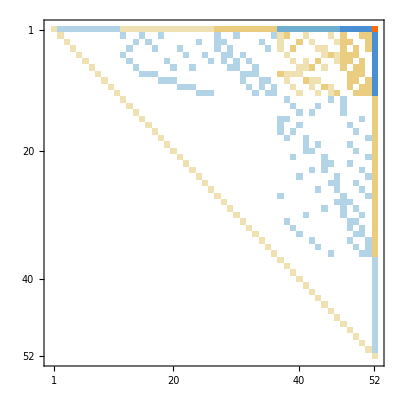

```mathematica
matie//MatrixPlot
```

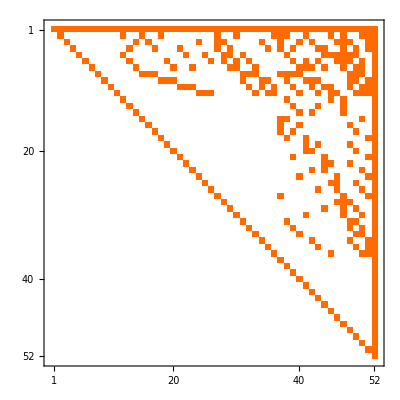

```mathematica
Inverse[matie]//MatrixPlot
```

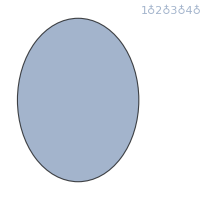
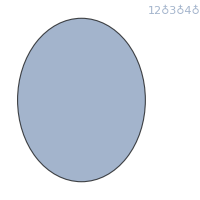

```mathematica
Table[FormulaGraph[allGraphs5[FindComplement[k,allGraphs5],"colofour"]],{k,Take[base1,2]}]
```

```mathematica
compbase1=Table[FindComplement[k,allGraphs5],{k,base1}]
```

{29524,49207,56011,58288,56770,56012,51475,52232,51478,49963,49972,49216,49220,49210,49208,36085,38281,39014,38308,36817,36898,36166,36194,36112,36086,31711,32441,32684,31954,31984,31738,31714,30253,30496,30586,30334,30262,29767,29857,29888,29797,29768,29605,29633,29608,29551,29560,29533,29537,29527,29525,59048}

```mathematica
Table[allGraphs5[k,"graph"],{k,compbase1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

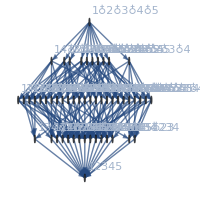
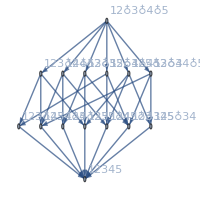
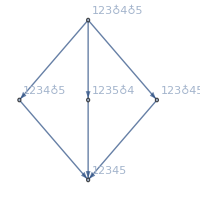
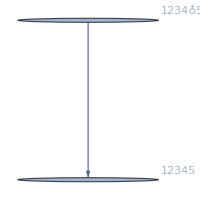
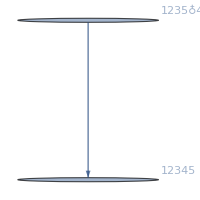

```mathematica
Table[FormulaGraph[allGraphs5[k,"colofourrealnull"]],{k,Take[compbase1,5]}]
```

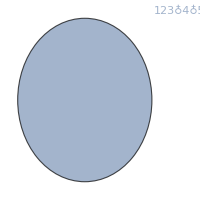
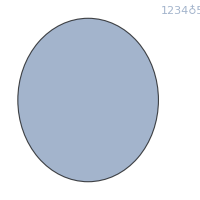
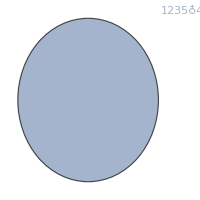
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[FormulaGraph[allGraphs5[k,"colofour"]],{k,Take[compbase1,5]}]
```

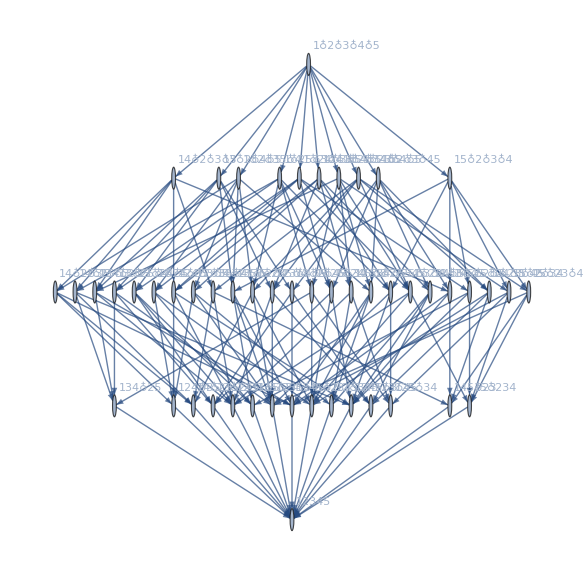
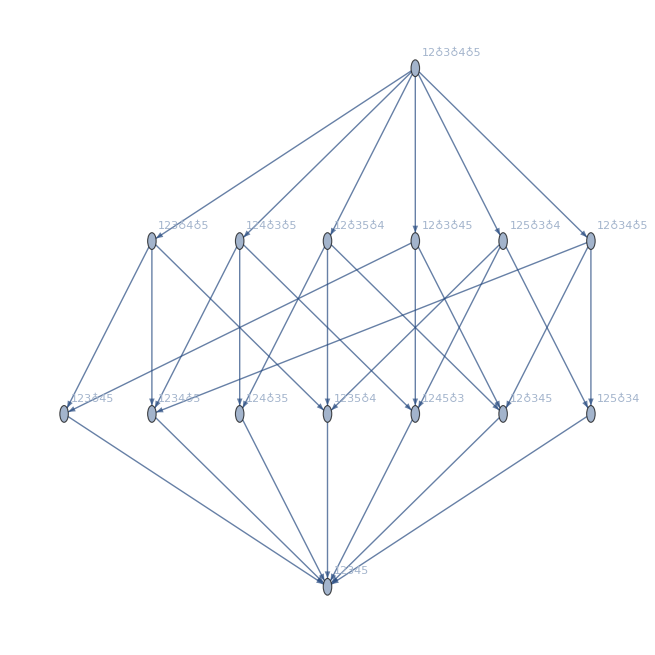

```mathematica
Table[FormulaGraph[allGraphs5[k,"colofour"]],{k,Take[base1,2]}]
```

## EMpty equivalent

```mathematica
Select[ListofVars[allGraphs5[K5Key,"colofourrealnull"]],StringCount[SymbolName[#],"x"]==4&]
```

{n1x2x3x4x5}

```mathematica
symsEMpt=Select[ListofVars[allGraphs5[K5Key,"colofourrealnull"]],StringCount[SymbolName[#],"x"]==1&]
```

{n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345}

```mathematica
base2=Select[Keys[allGraphs5],With[{vars=ListofVars[allGraphs5[#,"colofourrealnull"]]},
MemberQ[vars,n1x2x3x4x5]&&MemberQ[vars,n12345]&&(Fold[Or,Table[Sort[Intersection[vars,s]]==Sort[s],{s,Subsets[symsEMpt,{9}]}]])]&]//DeleteDuplicates
```

$Aborted

## kol kk

```mathematica
Map[Length,Sort[Map[Last,Table[RedBlueGreen[k,allGraphs5],{k,base1}]],Length[#1]<Length[#2]&]]
```

{0,37,37,37,37,37,37,37,37,37,37,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51}

```mathematica
TableForm[Tally[Map[Length,Sort[Map[Last,Table[RedBlueGreen[k,allGraphs5],{k,base1}]],Length[#1]<Length[#2]&]]],TableDepth->1]
```

{0,1}
{37,10}
{47,25}
{50,15}
{51,1}

```mathematica
RedBlueGreen
```